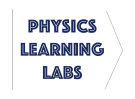
# -Graphics- Lab 8 - Pendulum Dynamics

Be sure to select Enable Dynamics for this notebook        -Graphics-

## Background

Depicted in Fig.(1) is a physical pendulum consisting of a rod, two brass cylinders, and a rotary motion sensor.  The pendulum rotates about an axis through point P.

```mathematica
-Graphics-      -Graphics-
```

The motion of the physical pendulum can be completely described by θ(t) and dθ/dt, i.e. its angle and angular velocity. These functions are governed by the nonlinear differential equation

(d^2 θ)/dt^2=(-m g h)/I sinθ,

which models a physical pendulum where m= pendulum mass, g= gravitational acceleration, I= moment of inertia about axis through P, h = center of mass length, and θ= angular displacement relative to the vertical.

If the angular displacement is small (θ<<1) then sinθ≈θ and Eq.(1) becomes

(d^2 θ)/dt^2=(-m g h)/I θ.

Eq.(2) is considered the linear (or harmonic) approximation to Eq.(1) and has the simple solution:

θ(t) = A cos(ωt + ϕ).

Here A is the amplitude, ω=(mgh/I)^(1/2) is the angular frequency, and ϕ is the phase which is determined by the initial conditions θ_0 and dθ/dt|_(t=0).

In the Simulation section, we will use Mathematica to solve Eq.(2) numerically, where we may explore the behavior under variation of ω and initial conditions. In the Experiment section, we will experimentally determine the dependence of the period T on the initial amplitude θ_0.

## Experiment

### Procedure

We will use the rotary motion sensor within Capstone to record θ(t) for the configurations shown in Fig.(2). For each configuration, the initial amplitude and average period of oscillation will be measured and recorded within period and theta0 below.

```mathematica
{{-Graphics-, -Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-, -Graphics-}}
```

Power on the Pasco 850 Universal Interface and open Lab_8.cap

Execute procedure steps 1-6 for trials 1-6.

1). Bring the pendulum to equilibrium position as shown in Fig.(2). In the state, the pendulum should be static. Press record within Capstone.

2). Displace the pendulum to the desired angle according to Fig.(2). Release the pendulum from rest. As you are displacing the pendulum with Capstone recording, you must be careful to not impart an initial angular velocity to the pendulum upon the release.

3). Record at least 10 total oscillations of data.

4). As a first step towards finding the period of oscillation, select the Add Coordinates/Delta Tool  
Locate the coordinate cursor tool on the graph and Right Click > Show Delta Tool   . Use the two coordinates to find the Δt corresponding to the first and last peak of your data. (Refer to Fig.(3) for an example).

5). Find the average period via T=Δt/(n-1), where n denotes the total number of peaks selected. Record the period T within the list period below. (For example, in Fig.(3) Δt=47.262 and n=13).

6). Based on the coordinate measurement of the first peak, record the initial amplitude θ_0 within the list theta0 below; for example, in Fig.(3) this would be 2.461 rad. The ordering of elements within period must match the ordering within theta0.

```mathematica
period =
```

```mathematica
theta0 =
```

### Plotting

Plot the dependence of period on initial amplitude below. We will continue analysis of this plot in the Analysis section.

```mathematica
myplot=ListPlot[Transpose[{theta0,period}],AxesLabel->{"θ_0 (rad)","T (s)"},Joined->True,PlotMarkers->"●",ImageSize->Large]
```

## Simulation

As mentioned in the background, we will utilize Mathematica’s numerical differential equation solver NDSolve to determine the solution of Eq.(1). The solution to Eq.(2) does not require numerical integration and has already been given as Eq.(3).

There are three parameters we may vary: the initial amplitude θ_0, the initial angular velocity dθ/dt|_(t=0), and the angular frequency ω.

The function θ(t) may be plotted as either
a)  The solution to the full nonlinear differential equation (Eq.(1))
b) The solution to the linear (harmonic) approximation of Eq.(1).

In addition, we can plot the trajectory of the pendulum through “phase space”. The physical pendulum represents a system with two degrees of freedom: the angle θ and the angular velocity dθ/dt (or more generally momentum). Determination of θ and dθ/dt at any moment in time completely specifies the state of the system. In plotting θ vs. dθ/dt, the pendulum fills outs a specific trajectory in phase space that is uniquely determined by the initial conditions. By looking at the phase space diagram, we can naturally characterize the state and behavior of the pendulum system.

Explore the behavior of θ(t) and phase space by varying the given parameters. Use this simulator to complete specific instructions and questions presented in the Analysis section.

```mathematica
Manipulate[
tmax=10;
nODE=Evaluate[{θ[t],θ'[t]}/.NDSolve[{θ''[t]==-ω^2 Sin[θ[t]],θ'[0]==ω0,θ[0]==θ0},{θ,θ'},{t,0,tmax}]];
lODE0=Evaluate[{θ[t]}/.DSolve[{θ''[t]==-ω^2 θ[t],θ'[0]==ω0,θ[0]==θ0},θ[t],t]];
lODE1=D[lODE0,t];
Column[{
Plot[{lODE0,nODE[[1]][[1]]},{t,0,tmax},PlotStyle->{Thickness[lODEth],Thickness[nODEth]},ImageSize->Large,AxesLabel->{"t (s)","θ (rad)"},GridLines->gridc],
If[phaseSp,ParametricPlot[{Flatten[{lODE1,lODE0}],Flatten[{nODE[[1]][[2]],nODE[[1]][[1]]}]},{t,0,tmax},PlotStyle->{Thickness[lODEth],Thickness[nODEth]},ImageSize->Large,AxesLabel->{"dθ/dt (rad/s)","θ (rad)"},PlotLabel->"Phase Space",GridLines->gridc],]
}],
Column[{
Control[{{gridc,None,"Gridlines"},{{Range[-20,20],Automatic}->"Show",None->"Hide"}}],
Control[{{lODEth,Large,"Linear Solution" ColorData[97,"ColorList"][[1]]},{Large->"Show",10^(-5)->"Hide"}}],
Control[{{nODEth,Large,"Nonlinear Solution"ColorData[97,"ColorList"][[2]]},{Large->"Show",10^(-5)->"Hide"}}],
Control[{{phaseSp,False,"Phase Space"},{True->"Show",False->"Hide"}}]
}],
Spacer[200],Delimiter,Spacer[200],
{{θ0,1.8,"θ_0"},0,π,0.1,Appearance->"Open"},
{{ω0,2.8,"dθ"},0,10,0.1,Appearance->"Open"},
{{ω,2.3,"ω"},0,10,.1,Appearance->"Open"},
ControlPlacement->{Left,Left},ContinuousAction->Automatic]
```

## Analysis

(d^2 θ)/dt^2=(-m g h)/I sinθ,

(d^2 θ)/dt^2=(-m g h)/I θ

θ(t) = A cos(ωt + ϕ).

### Linear/Nonlinear Solution Simulator

For a given ω, set dθ/dt|_(t=o)=0.

a)  Use the simulator to determine approximately what range of θ_0 yields close agreement between the nonlinear and linear solution. Express this range for θ_0 below.

b) How does this range of θ_0 relate to the approximation we made in deriving Eq.(2)?

c) As the agreement between the nonlinear and linear solutions diverges, what happens to the phase space trajectories? Look at large θ_0 in particular.

Set θ=0.5 rad and ω=4 rad/s. Starting from zero, slowly increase  dθ/dt|_(t=o) until a new behavior emerges. What happens to the nonlinear solution? Physically describe the behavior of the pendulum in this configuration.

A bound state is a configuration where the pendulum is bound between two maximum angles; for example θ may oscillate between [-20°, 20°]. An unbound state has no bound; for example, θ may takes the values [0,∞).

a)  Is there a set of parameters by which the nonlinear solution exhibits unbound motion?

b) Does the linear solution demonstrate a bound or unbound state? Does this make physical sense for large dθ/dt|_(t=o)? Why or why not?

c) By looking at the phase space diagram, what does a bound state look like? What about an unbound state?

### T(θ_0) Experiment

Paste an image of the plot T(θ_0) below

Paste an image of the both θ(t) and phase space for Trial 6 below.

Based on your experiment, under what range of θ_0 is the period approximately constant (or slowly varying)? Compare this result to the range of θ_0 in Q1a.

Based on your experimental data and physical reasoning, what do you predict happens to the period in the  lim_(θ_0→π)  ?

For any given trial, we may note that the amplitude decays over time.

a) What are possible causes of this decay?

b) How is the decay illustrated in reference to the phase space diagram?

How do the phase space diagrams change with respect to θ_0?

Contrast the experimental phase space diagrams to those of the simulator and justify the reasoning behind the observed differences.

### Bonus

Is it possible to balance the pendulum at the stationary equilibrium point θ=π? Why or why not? Try it!

# Submit this completed notebook as a .pdf into HuskyCT. (Make sure all cells sections are visible to receive credit for all your output. As a shortcut, use CTRL+A then CTRL+SHIFT+[ to open all cell sections).

## Image Credit: Haláček J., Ledvinka T. (2014) Analytical Conformal Compactification of Schwarzschild Spacetime. In: Bičák J., Ledvinka T. (eds) Relativity and Gravitation. Springer Proceedings in Physics, vol 157. Springer, Cham